### Tree Guess

```mathematica
Valuation[n_,p_]:=Valuation[n,p]=IntegerExponent[Abs[Numerator[n]],p]-IntegerExponent[Denominator[n],p]
```

```mathematica
SetAttributes[Valuation,Listable]
```

```mathematica
IsConstant[seq_]:= Length[Union[seq]]==1
```

```mathematica
SeqSplit[seq_,p_,offset_]:=Table[seq[[k]],{k,offset+1,Length[seq],p}]
```

```mathematica
Locate[coords_,seq_,p_]:= Module[{coords1=coords,list=seq,head},
While[coords1≠{},
head = coords1[[1]];
coords1=Drop[coords1,1];
list=SeqSplit[list,p,head]
];
list
]
```

```mathematica
TreeGuess[seq_,p_]:=Module[{tree={},queue={{}},node,ref},
While[queue≠ {},
node=queue[[1]];
queue=Drop[queue,1];
ref=Locate[node,seq,p];
If[IsConstant[ref],
tree=Join[tree,{{node,ref[[1]]}}],
queue=Join[queue,Table[Append[node,k],{k,0,p-1}]]
];
];
tree
]
```

### Automatic Sequence Guesser

```mathematica
PullSequence[F_,p_,coords_,values_]:=Module[{k=Length[coords],start},
start=Mod[Sum[coords[[n]]*p^(n-1),{n,1,k}],p^(k)];
Table[F[start+n*p^k],{n,0,values-1}]
]
```

```mathematica
AutomaticSequenceGuess[F_,branches_,values_,maxDepth_]:=Module[
{graph={},(*a list of coordinates paired with their corresponding outgoing edges in the form of {digit,name of target}*)
store={},(*list of sequences encountered already*)
names={},(*names of nodes corresponding to sequences seen*)
queue={{}},(*coordinates remaining to check*)
depth=0,(*length of largest coordinate -> how far down the tree goes before recursing or before the computation quits*)
coords,(*coordinates currently being checked*)
list,(*subsequence corresponding to coordinates being checked*)
name,(*name corresponding to current coordinates*)
position (*where to find the name of a node when a match is found*)
},
While[depth≤ maxDepth && queue≠{},
depth=Max[Table[Length[queue[[n]]],{n,1,Length[queue]}]]; 
coords=queue[[1]];
name=coords;
queue=Drop[queue,1];
list=PullSequence[F,branches,coords,values];
position=Position[store,list];
If[position≠{},(*thus it has been seen already*)
AppendTo[graph,{Drop[name,-1],{Last[coords],names[[position[[1,1]]]]}}],
AppendTo[store,list];
AppendTo[names,name];
queue=Join[queue,Table[Append[coords,k],{k,0,branches-1}]];
graph=If[name=={},graph,AppendTo[graph,{Drop[name,-1],{Last[name],name}}]
];
];
];
graph
]
```

```mathematica
CalcStart[F_,seq_,p_]:=If[seq=={},0,Mod[Sum[seq[[n]]*p^(n-1),{n,1,Length[seq]}],p^(Length[seq])]]
```

### Rendering the Trees

```mathematica
MakeVertexLabel[list_]:=StringJoin[ToString/@Riffle[Join[{"a"},list],"_"]]
```

```mathematica
Edges[graph_]:=DeleteDuplicates[Table[MakeVertexLabel[graph[[n,1]]]->MakeVertexLabel[graph[[n,2,2]]],{n,1,Length[graph]}]]
```

```mathematica
MakeEdgeLabels[graph_]:=Module[{position,edgelabel,from,to,pair,pairs={},label,
edgelabels={},i=0},
While[i< Length[graph],
i=i+1;
from=graph[[i,1]];
to=graph[[i,2,2]];
label=graph[[i,2,1]];
pair={from,to};
position=Position[pairs,pair];
If[position≠{},
AppendTo[edgelabels[[position[[1,1]],2]],label],
AppendTo[pairs,pair];
AppendTo[edgelabels,Labeled[MakeVertexLabel[from]->MakeVertexLabel[to],{label}]];
];
];
edgelabels
]
```

## Testing Grounds

### Tree Guesser(periodic only)

```mathematica
Table[1+(-1)^k,{k,1,100}]
```

{0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2,0,2}

```mathematica
TreeGuess[Table[1+(-1)^k,{k,1,100}],2]
```

{{{0},0},{{1},2}}

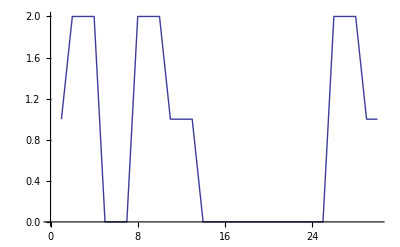

```mathematica
ListLinePlot[Table[Mod[CatalanNumber[n],3],{n,1,30}]]
```

### Automatic Sequence Guesser (better one)

```mathematica
MakeEdgeLabels[AutomaticSequenceGuess[Mod[#,3]&,3,100,4]]
```

AppendTo::rvalue: pairs$726 is not a variable with a value, so its value cannot be changed.

General::stop: Further output of AppendTo :: rvalue will be suppressed during this calculation.

Part::partw: Part 13 of {{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Riffle::list: List expected at position 1 in Riffle[{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}} ⟦ 13, 1 ⟧, ","].

Riffle::list: List expected at position 1 in Riffle["{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}}[[13,1]]", ","].

StringJoin::string: String expected at position 1 in StringJoin[Riffle["{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}}[[13,1]]", ","]].

Riffle::list: List expected at position 1 in Riffle[{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}} ⟦ 13, 2, 2 ⟧, ","].

General::stop: Further output of Riffle :: list will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[Riffle["{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}}[[13,2,2]]", ","]].

{->0{0},->1{1},->2{2},0->0{0},0->0{1},0->0{2},1->1{0},1->1{1},1->1{2},2->2{0},2->2{1},2->2{2},StringJoin[Riffle[{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}}[[13,1]],,]]->StringJoin[Riffle[{{{}, {0, {0}}}, {{}, {1, {1}}}, {{}, {2, {2}}}, {{0}, {0, {0}}}, {{0}, {1, {0}}}, {{0}, {2, {0}}}, {{1}, {0, {1}}}, {{1}, {1, {1}}}, {{1}, {2, {1}}}, {{2}, {0, {2}}}, {{2}, {1, {2}}}, {{2}, {2, {2}}}}[[13,2,2]],,]]{{{{},{0,{0}}},{{},{1,{1}}},{{},{2,{2}}},{{0},{0,{0}}},{{0},{1,{0}}},{{0},{2,{0}}},{{1},{0,{1}}},{{1},{1,{1}}},{{1},{2,{1}}},{{2},{0,{2}}},{{2},{1,{2}}},{{2},{2,{2}}}}⟦13,2,1⟧}}

```mathematica
AutomaticSequenceGuess[Mod[CatalanNumber[#],4]&,2,100,6]
```

{{{},{0,{0}}},{{},{1,{}}},{{0},{0,{0}}},{{0},{1,{0,1}}},{{0,1},{0,{0,1}}},{{0,1},{1,{0,1,1}}},{{0,1,1},{0,{0,1,1}}},{{0,1,1},{1,{0,1,1}}}}

```mathematica
?Convolve
```

RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "]"}] gives the convolution with respect to StyleBox["x", "TI"] of the expressions StyleBox["f", "TI"] and StyleBox["g", "TI"].
RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives the multidimensional convolution.

```mathematica
AutomaticSequenceGuess[Mod[#,3]&,3,100,4]
```

{{{},{0,{0}}},{{},{1,{1}}},{{},{2,{2}}},{{0},{0,{0}}},{{0},{1,{0}}},{{0},{2,{0}}},{{1},{0,{1}}},{{1},{1,{1}}},{{1},{2,{1}}},{{2},{0,{2}}},{{2},{1,{2}}},{{2},{2,{2}}}}

```mathematica
Table[Mod[10^n,7],{n,0,12}]
```

{1,3,2,6,4,5,1,3,2,6,4,5,1}

```mathematica
Derangements[n_]:=Derangements[n]=n!Sum[(-1)^k/k!,{k,0,n}]
```

```mathematica
Table[Valuation[Derangements[n],3],{n,2,100}]
```

{0,0,2,0,0,2,0,0,4,0,0,2,0,0,2,0,0,5,0,0,2,0,0,2,0,0,5,0,0,2,0,0,2,0,0,4,0,0,2,0,0,2,0,0,6,0,0,2,0,0,2,0,0,5,0,0,2,0,0,2,0,0,4,0,0,2,0,0,2,0,0,5,0,0,2,0,0,2,0,0,6,0,0,2,0,0,2,0,0,4,0,0,2,0,0,2,0,0,5}

```mathematica
list=AutomaticSequenceGuess[Valuation[Derangements[#],3]&,3,50,4];
Table[PullSequence[Valuation[Derangements[#],3]&,3,list[[n]][[1]],50],{n,1,Length[list]}]
```

$Aborted

{}

```mathematica
list=AutomaticSequenceGuess[Valuation[Derangements[#],3]&,3,20,5];
```

```mathematica
Convert[list]
```

Convert[{{{},{0,{0}}},{{},{1,{1}}},{{},{2,{0}}},{{0},{0,{0}}},{{0},{1,{0}}},{{0},{2,{0}}},{{1},{0,{1,0}}},{{1},{1,{1,1}}},{{1},{2,{1,1}}},{{1,0},{0,{1,0,0}}},{{1,0},{1,{1,0,1}}},{{1,0},{2,{1,0,2}}},{{1,1},{0,{1,1}}},{{1,1},{1,{1,1}}},{{1,1},{2,{1,1}}},{{1,0,0},{0,{1,0,0,0}}},{{1,0,0},{1,{1,0,0,1}}},{{1,0,0},{2,{1,0,0,1}}},{{1,0,1},{0,{1,0,1}}},{{1,0,1},{1,{1,0,1}}},{{1,0,1},{2,{1,0,1}}},{{1,0,2},{0,{1,0,0,1}}},{{1,0,2},{1,{1,0,2,1}}},{{1,0,2},{2,{1,0,0,1}}},{{1,0,0,0},{0,{1,0,0,0,0}}},{{1,0,0,0},{1,{1,0,0,0,1}}}}]

```mathematica
Valuation[Derangements[CalcStart[{1,0,2},3]],3]
```

IntegerExponent[Abs[CalcStart[{1,0,2},3]! Gamma[1+CalcStart[{1,0,2},3],-1]],3]-IntegerExponent[ⅇ Gamma[1+CalcStart[{1,0,2},3]],3]

```mathematica
PullSequence[Valuation[Derangements[#],3]&,3,{1,0,2},50]
```

{5,6,5,5,6,5,5,7,5,5,6,5,5,6,5,5,7,5,5,6,5,5,6,5,5,8,5,5,6,5,5,6,5,5,7,5,5,6,5,5,6,5,5,7,5,5,6,5,5,6}

### Rendering Trees

```mathematica
M=AutomaticSequenceGuess[Mod[#,2]&,2,100,6]
```

{{{},{0,{0}}},{{},{1,{1}}},{{0},{0,{0}}},{{0},{1,{0}}},{{1},{0,{1}}},{{1},{1,{1}}}}

```mathematica
Graph[MakeEdgeLabels[M]]
```

-Graphics-